given a table of n values

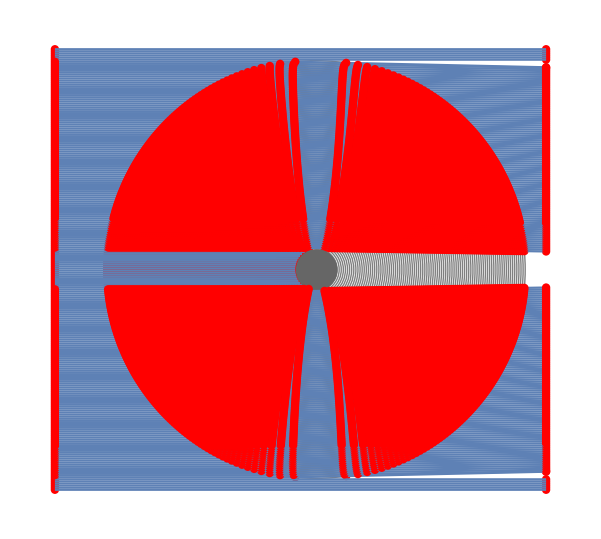

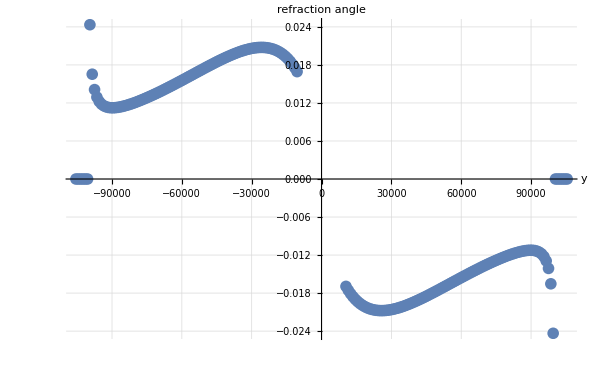

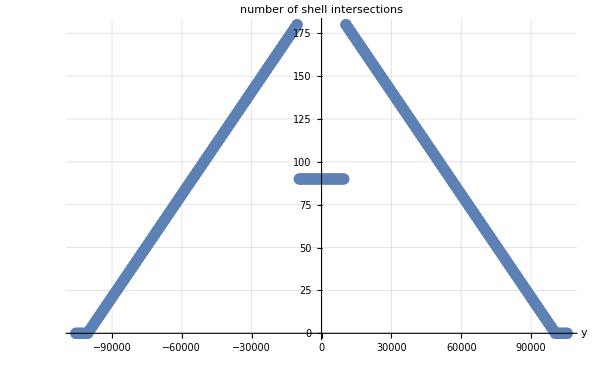

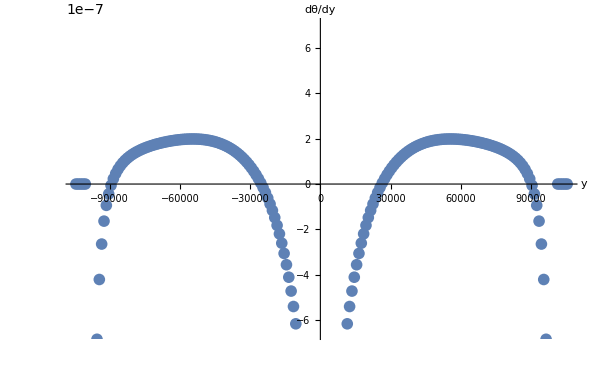

```mathematica
Clear["Global`*"];
startTime = DateString[];

(* Assumptions:
 shells are located around the origin
light rays never bend more than 90 degrees
*)

(* local gravity as a function of r *)
Gravity[r_]:=G*MPluto/r^2;

(* pressure as a function of height *)
Pressure[p0_,M_,h_,T_]:=p0 E^((-M Gravity[h+rSurf] h)/(k T));

(* Lorentz-Lorenz Equation for n values close to 1: returns a refractive index n given a temperature and pressure*)
LorentzLorenz[α_,p_,T_]:=√(1+(4π NAvagadro α p)/(R T)); 

(* shells are composed of the following: the circle graphic, the circle equation, the circle radius, the n value *)
(* more will be added to shells as we get into physical properties *)
Shell[r_,n_]:={Circle[{0,0},r],x^2+y^2==r^2,r,n}; 

(* calculate the normal angle of a shell based on location, assuming shells centered at 0,0) *)
NormalAngle[point_]:=ArcTan[point[[1]],point[[2]]]; 

(* refraction as a function of angles and rafractivity indicies *)
SnellsLaw[θin_,nin_,nout_]:=
If[nin == nout,
θin,
ArcSin[Sin[θin]nin/nout]
];

(* make an atmosphere with linearly-spaced shells specified by minimum, maximum, and step size of radius *)
MakeAtmosphere[min_,max_,step_,nTable_]:=Module[{r,center,nMax,nStep,n,i},
atmosphere={};

Which[
(* if nTable is null, use a linearly-varying n with nMax == 1.01 *)
((Length[nTable]==0)),
{
Print["not given a table of n values"];
If[nTable==Null,
nMax = 1.01;
];
If[NumberQ[nTable],
nMax = nTable;
];

nStep = (nMax-1.)/((max-min+1)/step); (*+1 is to ensure that the outer shell doesn't have n = 1.0 *)
n = nMax;
Do[
{
atmosphere =Append[atmosphere,Shell[r,n]];
n-=nStep;
},
{r,min,max,step}
];
},

True,
(* we're actually given a table of n values *)
{
Print["given a table of n values"],
i = 1;
Do[
{
n=nTable[[i]];
atmosphere =Append[atmosphere,Shell[r,n]];
i+=1;
},
{r,min,max,step}
];
}
]
]

(* make the graphics objects *)
MakeAtmosphereGraphic[atm_]:=Table[Graphics[{Opacity[0.5],atmosphere[[i,1]]}],{i,1,Length[atm]}];

MakeIntersectionsPointsGraphic[intersections_]:=Graphics[{Red,Point[Table[{x/.intersections[[i]],y/.intersections[[i]]},{i,Length[intersections]}]]}];

FindNextShellIntersection[radius_,rayPosition_,rayAngle_]:=Module[{x0,y0,m,t1,t2,tList},
x0 = rayPosition[[1]];
y0 = rayPosition[[2]];
m=Tan[rayAngle];
t1 = (-x0-m y0 + √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
t2 = (-x0-m y0 - √(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);

(* return only real positive time values *)
tList=Select[{t1,t2},(#∈Reals&&#>TOL)&]
]

(* function that identifies where the light currently is in relation to shells *)
LocateLightRay[position_,atm_]:=Module[{shellRadii,posRadius,difference,shellNum},
{
shellRadii = atm[[All,3]];
posRadius = Norm[position];
Which[
(* entirely outside of shells *)
posRadius > Last[shellRadii],
rayLocation = "outside",

(* entirely inside the inner shell *)
posRadius < First[shellRadii],
rayLocation = "inside",

(* on outer shell *)
Abs[Last[shellRadii]- posRadius]<TOL,
rayLocation = "on outer shell",

True,
{
Do[
difference = Abs[posRadius-shellRadii[[i]]];
If[difference<TOL,
shellNum = i;
rayLocation="on";
Break[];,
rayLocation = "between";
];,
{i,Length[atm]}
]
}
]
};
rayLocation
]

(* updates the light position based on current position, direction, and shells *)
MoveLightRay[rayPath_,rayAngle_,atm_]:=Module[{location,tList,intersect,t,n2,position,posRadius,shellNum,noIntersect},
extincted = False;
position = Last[rayPath];
posRadius = Norm[position];

location  = LocateLightRay[position,atm];
Which[
(* only need to check the outermost shell *)
location == "outside",
{
t = Min[FindNextShellIntersection[Last[atm][[3]],position,rayAngle]];
},

(* only need to check the innermost shell *)
location == "inside",
{
t = Min[FindNextShellIntersection[First[atm][[3]],position,rayAngle]];
},

(* only need to check the second-outermost and itself shell unless it's a one-shell atmosphere *)
location == "on outer shell",
{
If[Length[atm]>1,
(* if it's a multi-shell atmosphere *)
{
t = Min[Join[
FindNextShellIntersection[atm[[-2,3]],position,rayAngle],
FindNextShellIntersection[atm[[-1,3]],position,rayAngle]
]
];
},

(* else if it's a single-shell atmosphere *)
{
t = Min[FindNextShellIntersection[atm[[1,3]],position,rayAngle]];
}
]
},

(* need to check the previous, current, and next shells *)
location == "on",
{
Do[
If[Abs[posRadius-atm[[All,3]][[i]]]<TOL,
shellNum = i;
Break[];,
];,
{i,Length[atm]}
];

If[shellNum==1,
(* if on inner shell *)
{
(* TODO - this is the solid planet case *)
extincted = True;
t =0;

(*
t=Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle];
]
]
*)
},

(* if on some other shell *)
t = Min[Join[
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum-1,3]],position,rayAngle]
]
]
];
},

(* need to check the shells that it is between- now use currentShell as a counter *)
location == "between",
{
Print["warning: between atmosphere layers - this shouldn't really happen"];
shellNum =Length[atm];
While[atm[[shellNum,3]] > posRadius,
shellNum-=1; 
];
tList = Join[
FindNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
FindNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle]
];
t= Min[tList];
}
];

(* stuff to be done regardless of ray location case *)

(* check for non-intersection case *)
noIntersect = False;
If[t==Infinity,
If[Length[rayPath]==1,
noIntersect = True;
];
t=atmMax*1.1-position[[1]]; (* arbirary end point for the light beams 10% past the maximum atmosphere radius *)
];

intersect = {t+position[[1]],Tan[rayAngle ] t + position[[2]]};
position = intersect;

(* figure out which we're now interacting with *)
Do[
If[Abs[Norm[position]-atm[[All,3]][[i]]]<TOL,
(* get the refractivity of the shell *)
n2 = atm[[i,4]];
Break[];,

(* if we're not interacting with a shell, then we're back in vacuum with n2 = 1.0 *)
n2 = 1.0
];,
{i,Length[atm]}
];
If[!extincted,
AppendTo[intersectionPoints,position];
If[noIntersect,
AppendTo[angleList,0.0];,
AppendTo[angleList,Refract[intersectionPoints,angleList,n2]]; 
];
position
];
]

(* refract based on entry and shell conditions using Snell's Law *)
Refract[rayPath_,angles_,n2_]:=Module[{newAngle,position,prevPosition,θ1,θ2,angle,grazedShell},
(*Print["refract called at "<> ToString[Last[rayPath]] <> ", n1 = " <> ToString[currentN] <> ", n2 = " <> ToString[n2]];*)
position = Last[rayPath];
prevPosition = rayPath[[-2]];
angle = Last[angles];
grazedShell = False;
Which[
(* just grazed the top or bottom of a shell (no interaction), keep the angle the same *)
Abs[position[[1]]]<TOL,
{
newAngle = angle;
grazedShell = True;
Print["grazed shell with angle = " <> ToString[angle] <>" and starting y value of " <> ToString[yStart]];
},

(* hitting shell from outside in (radius decreasing) *)
Norm[position]<Norm[prevPosition],
{
(*Print["outside in"];*)

If [position[[2]]>0,
{ (* above the y = 0 line *)
(*Print[NormalAngle[position]/Degree];*)
θ1= Mod[π-NormalAngle[position]+angle,π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-π+θ2;
},
{ (* on or below the y = 0 line *)
θ1=Mod[NormalAngle[position]-π-angle,π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-π-θ2;
}
]
},

(* hitting shell from inside out *)
(Norm[position]>Norm[prevPosition]) || (Norm[position]== Norm[prevPosition]),
{
 (*Print["inside out"];*)

If[position[[2]]>0,
{ (* above the y = zero line *)
θ1=Mod[NormalAngle[position]-angle,π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]-θ2;
},
{ (* on or below the y = 0 line *)
θ1=Mod[angle-NormalAngle[position],π/2];
θ2=SnellsLaw[θ1,currentN,n2];
newAngle = NormalAngle[position]+θ2;
}
]
}
];
If[!grazedShell,
currentN=n2;
];

newAngle = Mod[newAngle,2*π];
(* TODO - probably more elegent way to do the angle formatting, because I basically want all angles to be near zero for readability *)
If[newAngle> 3*π/4,
newAngle = newAngle-2*π;
];
(*
Print[θ1/Degree];
Print[θ2/Degree];
Print[newAngle];
Print[""];
*)
newAngle
];

(*run the program starting here *)
(*declare variables *)

TOL = 10^-9;
plutoRadius = 9000;

(* physical constants *)
NAvagadro=6.022*10^23;  (* Avagadro's number *)
R=8.3145; (*J/mol K; universal gas constant*)
k = 1.3806488 ; (* m^2 kgs^-2 K^-1; Boltzmann constant *)
G = 6.67*10^-11; (* universal gravitational constant in mks units *)

αN2=1.71*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas *)
μN2=0.028; (* kg; molar mass of Subscript[N, 2] *)

(* assumed properties of Pluto *)
p0 = 0.3; (* N/m^2; assumed surface pressure of Pluto *)
T = 50.; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29*10^22; (* kg; mass of Pluto *)
rSurf = 11950000.; (* m; surface radius of Pluto *)

(* make the atmosphere *)
atmMin = 10000.;
atmMax = 100000.;
atmStep = 1000.;

(* check to make sure that the discretization is proper; if not, fix it *)
If[Mod[atmMax-atmMin,atmStep]≠0,
{
atmMax=Floor[atmMax/atmStep]*atmStep;
Print["warning: atmosphere discretization is not integer- maximum radius corrected to "<> ToString[atmMax]];
}
];

(* TODO putting in a dummy α value for now to produce results we can see *)
nTable = Table[LorentzLorenz[10^-23,Pressure[p0,μN2*10,h,T],T],{h,atmMin,atmMax,atmStep}];
MakeAtmosphere[atmMin,atmMax,atmStep,nTable];
(* TODO - using a linear thing for now *)

 startingY = {}; (* store starting y coordiate *)
totalRefraction = {}; (* store final angles from refraction *)
yVsRefraction = {}; (* store pairs of numbers of y and refraction angles *)
dθOverdy={}; (* store a difference element of the above *)
atmGraphics = {}; (* store the graphics generated by the atmosphere model and the light rays *)
numIntersectionPoints = {}; (* store the number of intersections encountered by each light ray *)

Do[
yMultTemp = PrintTemporary["y multiplicative factor " <> ToString[yMultFact]]; (* for tracking progress *)

(* make a light ray *)
yStart = atmMax*yMultFact;
origin = {-atmMax*1.25,yStart}; (* origin needs to be specified by doubles rather than ints *)
angle = 0;
currentN = 1.0;

(* initialize lists of data *)
intersectionPoints = {origin};
angleList = {angle};

MoveLightRay[intersectionPoints,Last[angleList],atmosphere]; (* move the light ray up to the first atmosphere encounter *)

extincted = False;
While[Norm[Last[intersectionPoints]]<= atmMax && !extincted,
(*rayTemp = PrintTemporary["(x,y) = "<>ToString[Last[intersectionPoints]] <> ", r = "<>ToString[Norm[Last[intersectionPoints]]]];*)
MoveLightRay[intersectionPoints,Last[angleList],atmosphere];
(*NotebookDelete[rayTemp];*)
];

(* put the results in the appropriate lists *)
If[!extincted,
AppendTo[startingY,yStart];
AppendTo[totalRefraction,Last[angleList]];
AppendTo[yVsRefraction,{yStart,Last[angleList]}];

If[Length[startingY]>1,
AppendTo[dθOverdy,{yStart,(totalRefraction[[-2]]-totalRefraction[[-1]])/ (startingY[[-2]]-startingY[[-1]])}];
];
];

AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[intersectionPoints]}],ListLinePlot[intersectionPoints]}];
AppendTo[numIntersectionPoints,{yStart,Length[intersectionPoints]-2}]; (* minus 2 for start and end points*)

NotebookDelete[yMultTemp];,

{yMultFact,-1.055,1.055,0.01}
]

(* graphics stuff starts here *)
plutoGraphic = Graphics[{GrayLevel[0.4],Disk[{0,0},atmMin]}];
Show[MakeAtmosphereGraphic[atmosphere],atmGraphics,plutoGraphic] (* shell graphic *)
ListPlot[yVsRefraction,AxesLabel->{"y","refraction angle"},GridLines->Automatic]
ListPlot[numIntersectionPoints,AxesLabel-> {"y","number of shell intersections" },GridLines->Automatic]
ListPlot[dθOverdy,AxesLabel->{"y","dθ/dy"}]


endTime = DateString;
Print["start: " <> startTime];
Print["end: " <> endTime];
```